```mathematica
Exit[];
```

```mathematica
PrependTo[$Path,"D:\\Users\\Johannes\\Promotion\\SVN Rep\\Mathematica\\Packages"];<<JoFin`
```

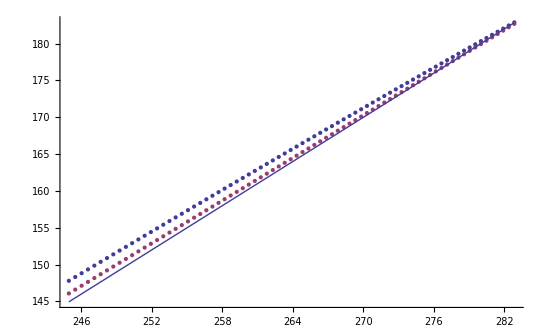

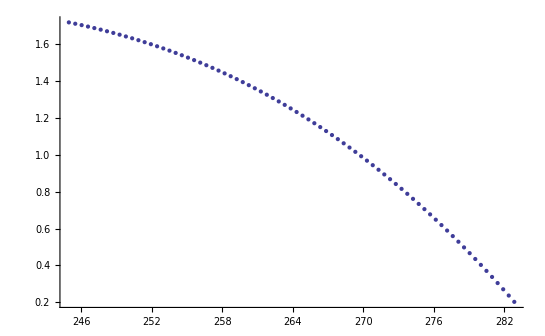

```mathematica
{σ,d}=IsometricGeometricAverageParameters[0.2,0,0.1,2];
r=0.05;T=2;k=100;a=Import["D:\\Users\\Johannes\\Promotion\\SVN Rep\\Programmierung\\Tridiagonal Solver Tests\\output\\a.txt","Table"];
nn=3Length[a]/4;
a=a[[nn;;]];
b={#[[1]],BlackScholesCall[#[[1]],k,T,r,σ,d]}&/@a;
Show[ListPlot[{a,b},PlotRange->All],Plot[Max[x -k,0],{x,Min[a[[;;,1]]],Max[a[[;;,1]]]}]]
ListPlot[Transpose[{a[[;;,1]],(a[[;;,2]]-b[[;;,2]])}],PlotRange->All]
```

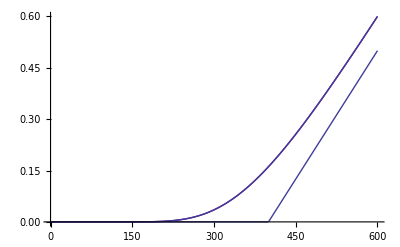

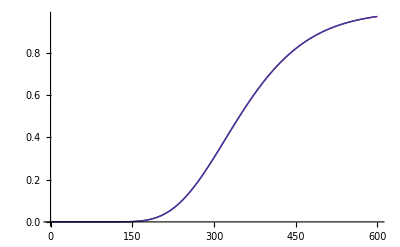

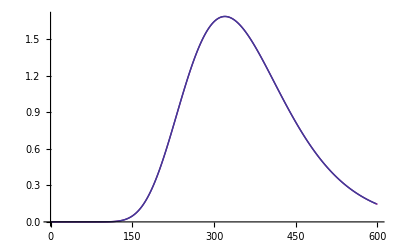

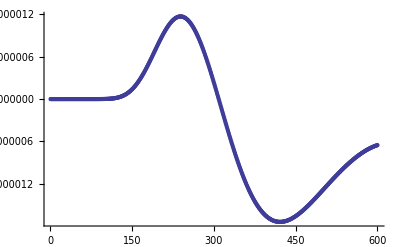

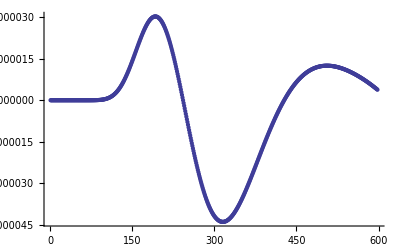

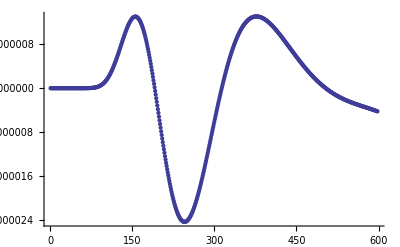

```mathematica
n=2000;nn=Round[1.5/5*n];h=5.0/n;
b=Table[BlackScholesCall[j 5.0/n,1.0,2.0,0.05,0.2,0],{j,1,nn}];
bS=Table[BlackScholesCallDelta[j 5.0/n,1.0,2.0,0.05,0.2,0],{j,2,nn-1}];
bSS=Table[BlackScholesCallGamma[j 5.0/n,1.0,2.0,0.05,0.2,0],{j,2,nn-1}];
Show[ListLinePlot[a[[;;nn]],PlotStyle->Purple],ListLinePlot[b],Plot[Max[x 5/n -1,0],{x,0,nn}]]
Show[ListLinePlot[CentralDifferences[a][[;;nn]]/h/2,PlotStyle->Purple],ListLinePlot[bS]]
Show[ListLinePlot[Differences[a,2][[;;nn]]/h^2,PlotStyle->Purple],ListLinePlot[bSS]]
ListPlot[(a[[;;nn]]-b)/Norm[b],PlotRange->All]
ListPlot[(CentralDifferences[a][[;;nn-2]]/h/2-bS)/Norm[bS],PlotRange->All]
ListPlot[(Differences[a,2][[;;nn-2]]/h^2-bSS)/Norm[bSS],PlotRange->All]
```